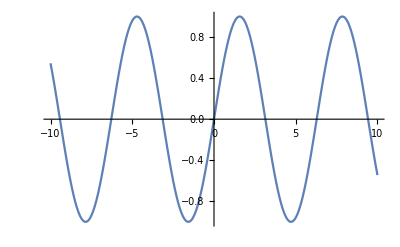

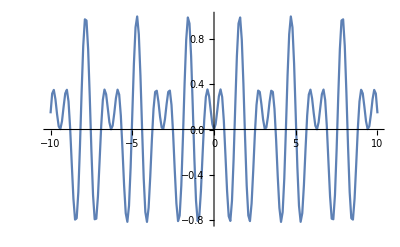

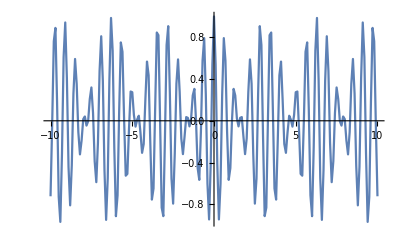

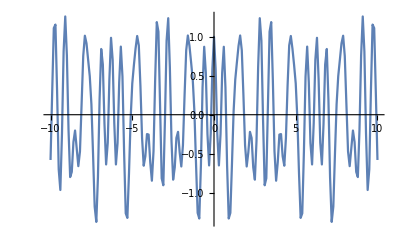

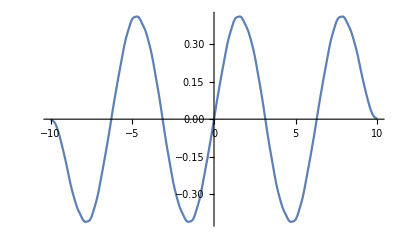

```mathematica
c1[x_]:=Sin[5x];
s1[x_]:=Sin[x];
c2[x_]:=Cos[10x];
s2[x_]:=Cos[x];
r:=Range[-10,10,.1];
c1p:=Map[c1,r]
s1p:=Map[s1,r]
c2p:=Map[c2,r]
s2p:=Map[s2,r]
ListLinePlot[{s1p},DataRange->{-10,10}]
ListLinePlot[{c1p*s1p},DataRange->{-10,10}]
ListLinePlot[{c2p*s2p},DataRange->{-10,10}]
ListLinePlot[{c1p*s1p+c2p*s2p},DataRange->{-10,10}]
ListLinePlot[{LowpassFilter[(c1p*s1p+c2p*s2p)*c1p,.1]},DataRange->{-10,10}]
```

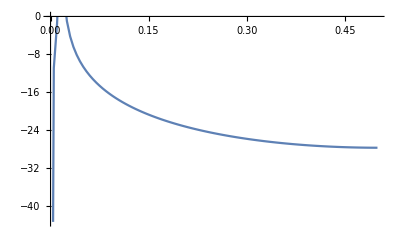

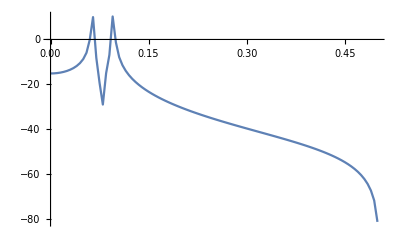

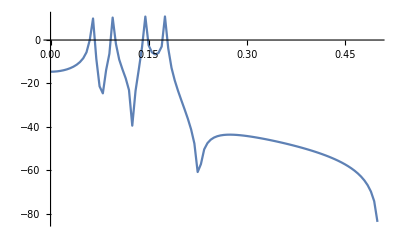

```mathematica
Periodogram[s1p]
Periodogram[c1p*s1p]
Periodogram[c1p*s1p+c2p*s2p]
```